```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ww0m1 = Import["ww0m1_angular.dat","List"];
ww01 = Import["ww01_angular.dat","List"];
ww10 = Import["ww10_angular.dat","List"];
wwm10 = Import["wwm10_angular.dat","List"];
ww00 = Import["ww00_angular.dat","List"];
ww11 = Import["ww11_angular.dat","List"];
wwm1m1 = Import["wwm1m1_angular.dat","List"];
ww1m1 = Import["ww1m1_angular.dat","List"];
wwm11 = Import["wwm11_angular.dat","List"];
(*dyt import*)
dytww00 = Import["ww00_angular_dyt015_new.dat","List"];
dytww11 = Import["ww11_angular_dyt015.dat","List"];
dytwwm1m1 = Import["wwm1m1_angular_dyt015.dat","List"];
mdytww00 = Import["ww00_angular_dytm015_new.dat","List"];
mdytww11 = Import["ww11_angular_dytm015.dat","List"];
mdytwwm1m1 = Import["wwm1m1_angular_dytm015.dat","List"];
```

```mathematica
(*dyt import*)
(*dytww11 = Import["ww111_angular.dat","List"];
dytwwm1m1 = Import["wwm1m1_angular_dyt0.1_1000.dat","List"];
dytww1m1 = Import["ww1m1_angular_dyt0.1_1000.dat","List"];
dytwwm11 = Import["wwm11_angular_dyt0.1_1000.dat","List"];*)
sqrtsList=Table[350+25*i,{i,0,400}];
thetaList=Table[0+(Pi/180)*i,{i,0,181}];
```

```mathematica
Length[mdytww00]
```

182

```mathematica
<<CustomTicks.m
ticks0=LogTicks[10,-3,6,TickLabelStep->1];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

```mathematica
factor=0.3894*10^12;
lineplot=ListLogPlot[{Transpose[{Cos[thetaList],factor*ww00}],Transpose[{Cos[thetaList],factor*ww01}],Transpose[{Cos[thetaList],factor*ww10}],Transpose[{Cos[thetaList],factor*ww11}],Transpose[{Cos[thetaList],factor*ww1m1}],Transpose[{Cos[thetaList],factor*wwm11}],Transpose[{Cos[thetaList],factor*(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}], Transpose[{Cos[thetaList],factor*dytww00}],Transpose[{Cos[thetaList],factor*dytww01}],Transpose[{Cos[thetaList],factor*dytww10}],Transpose[{Cos[thetaList],factor*dytww11}],Transpose[{Cos[thetaList],factor*dytww1m1}],Transpose[{Cos[thetaList],factor*dytwwm11}],Transpose[{Cos[thetaList],factor*(2 dytww11 + dytwwm11 +  dytww1m1 + 2 dytww10  + 2 dytww01 + dytww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["dσ/(dcos θ) (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["δ_yμ=0.1",Black,20],
PlotLegends->{Style[" W^-(0) W^+(0)",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{0.001,10000}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
(*customticks package*)
```

Transpose::nmtx: The first two levels of {{1,Cos[π/180],Cos[π/90],Cos[π/60],Cos[π/45],Cos[π/36],Cos[π/30],Cos[(7 π)/180],Cos[(2 π)/45],Cos[π/20],«172»},3.894×10^11 dytww01} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,Cos[π/180],Cos[π/90],Cos[π/60],Cos[π/45],Cos[π/36],Cos[π/30],Cos[(7 π)/180],Cos[(2 π)/45],Cos[π/20],«172»},3.894×10^11 dytww10} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,Cos[π/180],Cos[π/90],Cos[π/60],Cos[π/45],Cos[π/36],Cos[π/30],Cos[(7 π)/180],Cos[(2 π)/45],Cos[π/20],«172»},3.894×10^11 dytww1m1} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{1.,3.28435},{0.999848,3.29163},{0.999391,3.31314},{0.99863,3.34801},{0.997564,3.3949},{0.996195,3.45218},{0.994522,3.51807},{0.992546,3.59082},{0.990268,3.66878},{0.987688,3.7505},«172»},«9»,«4»} is not a list of numbers or pairs of numbers.

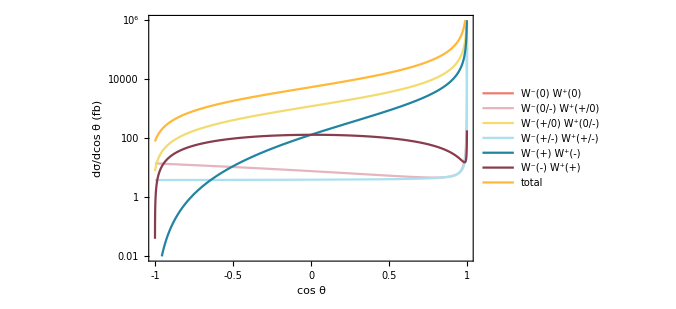

```mathematica
lineplot1=ListLogPlot[{-Transpose[{Cos[thetaList],factor*ww00}],Transpose[{-Cos[thetaList],factor*ww01}],Transpose[{-Cos[thetaList],factor*ww10}],Transpose[{-Cos[thetaList],factor*ww11}],Transpose[{-Cos[thetaList],factor*ww1m1}],Transpose[{-Cos[thetaList],factor*wwm11}],Transpose[{-Cos[thetaList],factor*(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["dσ/dcos θ (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["",Black,20],
PlotLegends->{Style[" W^-(0) W^+(0)",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{0.01,1000000}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
(*Export["WWtt_angular_partonic.pdf",lineplot1]
```

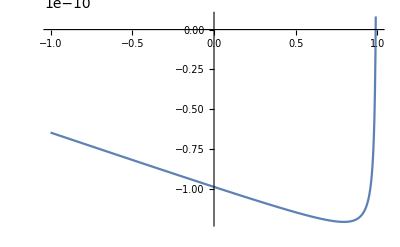

```mathematica
ListPlot[Transpose[{-Cos[thetaList],((*2 dytww11 -2 ww11  +*) dytww00- ww00)}],Joined->True]
```

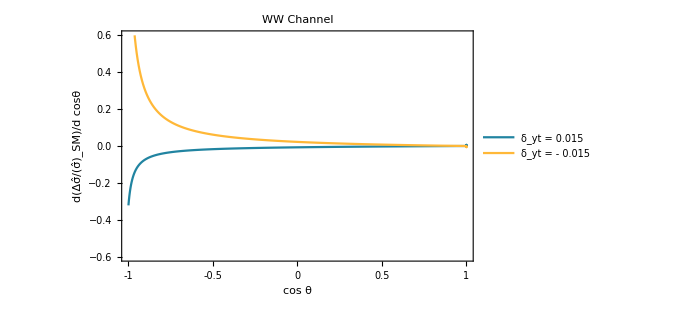

```mathematica
nonlinearlineplot3=ListPlot[{Transpose[{-Cos[thetaList],(2 dytww11 + dytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}],Transpose[{-Cos[thetaList],(2 mdytww11 + mdytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][6],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,17,FontFamily->"Times"],Style["d(Δσ̂/(σ̂)_SM)/d cosθ",Black,17,FontFamily->"Times"]},
PlotLabel->Style["WW Channel   ",Black,17,FontFamily->"Times"],
PlotLegends->Placed[{Style[" δ_yt =    0.015 ",Black,15,FontFamily->"Times"],Style[" δ_yt = - 0.015",Black,15,FontFamily->"Times"]},{0.3,0.8}],
PlotRange->{{-1,1},{-0.6,0.6}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

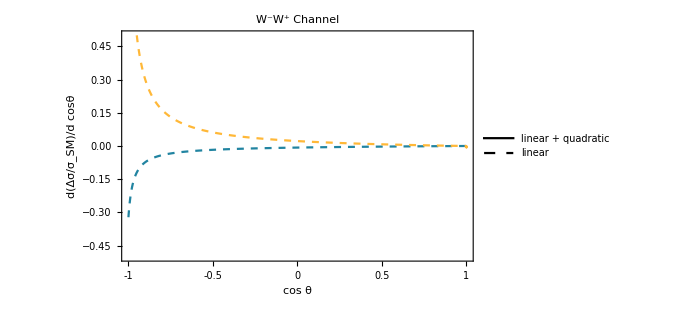

```mathematica
nonlinearlineplot3=ListPlot[{Transpose[{-Cos[thetaList],(2 dytww11 + dytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}],Transpose[{-Cos[thetaList],(2 mdytww11 + mdytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{Directive[ColorData[colorselecitonumber][6],Dashed],Directive[Dashed,ColorData[colorselecitonumber][2]]},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,17,FontFamily->"Times"],Style["d(Δσ/σ_SM)/d cosθ",Black,17,FontFamily->"Times"]},
PlotLabel->Style["W^-W^+ Channel",Black,17],
PlotLegends->Placed[LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["linear + quadratic",FontFamily->"Times",15],Style["linear",FontFamily->"Times",15]}],{0.72,0.8}],
PlotRange->{{-1,1},{-1/2,1/2}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

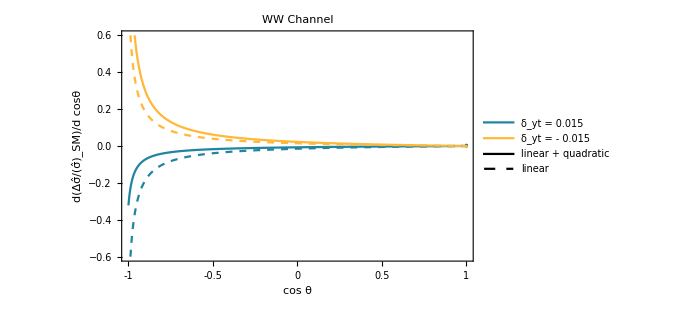

```mathematica
combinedcos = Show[nonlinearlineplot3, linearlineplot3]
```

```mathematica
Export["WWcombined_angular.pdf",combinedcos]
```

WWcombined_angular.pdf

```mathematica
(*Export["WWtt_angular_partonic_dyt2.pdf",lineplot3]
```

```mathematica
(*Export["WW_angular_1000_total.pdf",lineplot3]
```

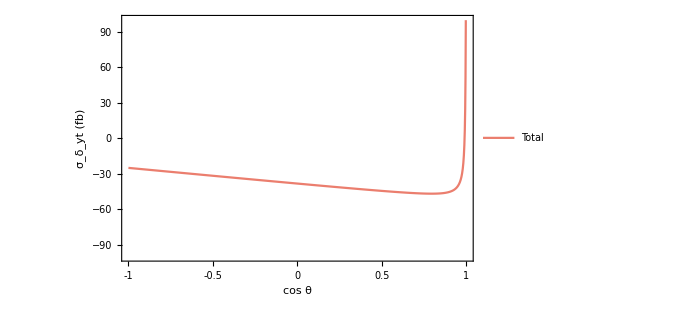

```mathematica
lineplot4=ListPlot[{Transpose[{-Cos[thetaList],factor*(2 dytww11 + dytww00-2 ww11  - ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["σ_δ_yt (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["",Black,20],
PlotLegends->{Style[" Total",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{-100,100}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
factor*(2 dytww11 + dytww00-2 ww11  - ww00)
```

{-25.0668,-25.0688,-25.075,-25.0852,-25.0995,-25.1179,-25.1403,-25.1669,-25.1975,-25.2321,-25.2708,-25.3135,-25.3602,-25.4109,-25.4656,-25.5243,-25.5869,-25.6535,-25.7239,-25.7982,-25.8764,-25.9585,-26.0443,-26.1339,-26.2273,-26.3244,-26.4252,-26.5297,-26.6377,-26.7494,-26.8647,-26.9834,-27.1057,-27.2314,-27.3605,-27.493,-27.6288,-27.7679,-27.9102,-28.0557,-28.2043,-28.3561,-28.5109,-28.6687,-28.8294,-28.9931,-29.1596,-29.3289,-29.5009,-29.6756,-29.8529,-30.0328,-30.2153,-30.4001,-30.5874,-30.777,-30.9688,-31.1629,-31.3591,-31.5574,-31.7577,-31.96,-32.1641,-32.3701,-32.5778,-32.7872,-32.9982,-33.2108,-33.4248,-33.6402,-33.8569,-34.0749,-34.2941,-34.5143,-34.7356,-34.9579,-35.181,-35.4049,-35.6296,-35.8549,-36.0807,-36.3071,-36.5338,-36.7609,-36.9882,-37.2157,-37.4432,-37.6707,-37.8982,-38.1255,-38.3525,-38.5791,-38.8053,-39.031,-39.2561,-39.4804,-39.704,-39.9266,-40.1483,-40.3689,-40.5883,-40.8064,-41.0232,-41.2384,-41.4521,-41.6641,-41.8743,-42.0827,-42.2889,-42.4931,-42.695,-42.8946,-43.0916,-43.2861,-43.4778,-43.6666,-43.8524,-44.035,-44.2143,-44.3901,-44.5622,-44.7306,-44.8949,-45.055,-45.2107,-45.3618,-45.508,-45.6491,-45.7848,-45.9148,-46.0389,-46.1567,-46.2679,-46.3719,-46.4685,-46.5571,-46.6373,-46.7084,-46.7698,-46.8208,-46.8607,-46.8885,-46.9032,-46.9038,-46.8889,-46.8572,-46.8069,-46.7361,-46.6426,-46.524,-46.3772,-46.1987,-45.9844,-45.7294,-45.4279,-45.0729,-44.656,-44.1666,-43.5921,-42.9167,-42.1203,-41.1779,-40.0569,-38.7151,-37.097,-35.1275,-32.7045,-29.6849,-25.8643,-20.9417,-14.46,-5.69706,6.54117,24.3448,51.6418,96.5259,177.869,348.064,796.092,2528.93,8033.3,2528.93}